```mathematica
t=0.001
```

0.001

```mathematica
v=(0.05*10^-3)/60
```

8.33333×10^-7

```mathematica
2 v t*10^9
```

1.66667

```mathematica
v
```

8.33333×10^-7

```mathematica
(632*10^-9)/(2 v)
```

0.3792

```mathematica
30/0.3792
```

79.1139

```mathematica
0.3792/6
```

0.0632

```mathematica
%/0.001
```

63.2

```mathematica
data=Import["/Users/benxgh1996/Desktop/interferometry/wl_data.csv"];
```

```mathematica
TableForm[%7]
```

1
 |  |  |  |

```mathematica
Length[data]
```

30000

```mathematica
data[[1]]
```

{ï»¿0,-1.2183}

```mathematica
data[[2]]
```

{0.001,-1.1841}

```mathematica
data[[1]][[1]]=0
```

0

```mathematica
data[[1]]
```

{0,-1.2183}

```mathematica
Last[data]
```

{29.999,-0.9106}

```mathematica
Part[data,1;;100]
```

{{0,-1.2183},{0.001,-1.1841},{0.002,-1.1523},{0.003,-1.167},{0.004,-1.2109},{0.005,-1.2231},{0.006,-1.2085},{0.007,-1.2109},{0.008,-1.2207},{0.009,-1.2256},{0.01,-1.2256},{0.011,-1.2231},{0.012,-1.2036},{0.013,-1.1914},{0.014,-1.2012},{0.015,-1.2207},{0.016,-1.2231},{0.017,-1.2207},{0.018,-1.2231},{0.019,-1.2134},{0.02,-1.1963},{0.021,-1.2012},{0.022,-1.2158},{0.023,-1.2231},{0.024,-1.2231},{0.025,-1.2256},{0.026,-1.2231},{0.027,-1.2109},{0.028,-1.2012},{0.029,-1.1987},{0.03,-1.1938},{0.031,-1.1841},{0.032,-1.1719},{0.033,-1.1694},{0.034,-1.1792},{0.035,-1.2036},{0.036,-1.2183},{0.037,-1.2207},{0.038,-1.2183},{0.039,-1.2036},{0.04,-1.1792},{0.041,-1.1694},{0.042,-1.1865},{0.043,-1.2061},{0.044,-1.2134},{0.045,-1.2085},{0.046,-1.1743},{0.047,-1.1157},{0.048,-1.0718},{0.049,-1.0791},{0.05,-1.1304},{0.051,-1.1694},{0.052,-1.1841},{0.053,-1.1694},{0.054,-1.1499},{0.055,-1.1401},{0.056,-1.1426},{0.057,-1.1597},{0.058,-1.1719},{0.059,-1.1621},{0.06,-1.1084},{0.061,-1.04},{0.062,-0.979},{0.063,-0.9717},{0.064,-1.0205},{0.065,-1.0791},{0.066,-1.1206},{0.067,-1.1304},{0.068,-1.1108},{0.069,-1.0913},{0.07,-1.0864},{0.071,-1.0986},{0.072,-1.106},{0.073,-1.0962},{0.074,-1.0522},{0.075,-0.9937},{0.076,-0.9595},{0.077,-0.9644},{0.078,-0.9863},{0.079,-1.0181},{0.08,-1.0205},{0.081,-0.9839},{0.082,-0.9375},{0.083,-0.918},{0.084,-0.9351},{0.085,-0.9766},{0.086,-0.9961},{0.087,-0.9814},{0.088,-0.9326},{0.089,-0.8838},{0.09,-0.8618},{0.091,-0.8765},{0.092,-0.9131},{0.093,-0.9277},{0.094,-0.8887},{0.095,-0.8276},{0.096,-0.7568},{0.097,-0.7202},{0.098,-0.73},{0.099,-0.769}}

```mathematica
Part[data,29900;;29999]
```

{{29.899,-1.1279},{29.9,-1.1084},{29.901,-1.1035},{29.902,-1.1206},{29.903,-1.1475},{29.904,-1.1694},{29.905,-1.1792},{29.906,-1.1816},{29.907,-1.1719},{29.908,-1.1719},{29.909,-1.1792},{29.91,-1.1938},{29.911,-1.2012},{29.912,-1.2012},{29.913,-1.2012},{29.914,-1.2012},{29.915,-1.2012},{29.916,-1.2134},{29.917,-1.2231},{29.918,-1.2256},{29.919,-1.2207},{29.92,-1.2134},{29.921,-1.2061},{29.922,-1.2061},{29.923,-1.2109},{29.924,-1.2207},{29.925,-1.228},{29.926,-1.2354},{29.927,-1.2427},{29.928,-1.25},{29.929,-1.25},{29.93,-1.2476},{29.931,-1.2476},{29.932,-1.25},{29.933,-1.25},{29.934,-1.2476},{29.935,-1.2476},{29.936,-1.25},{29.937,-1.2476},{29.938,-1.2354},{29.939,-1.2305},{29.94,-1.2378},{29.941,-1.2451},{29.942,-1.25},{29.943,-1.25},{29.944,-1.25},{29.945,-1.25},{29.946,-1.2476},{29.947,-1.2427},{29.948,-1.2427},{29.949,-1.2476},{29.95,-1.2427},{29.951,-1.2427},{29.952,-1.2378},{29.953,-1.2378},{29.954,-1.2378},{29.955,-1.2427},{29.956,-1.2451},{29.957,-1.2427},{29.958,-1.2354},{29.959,-1.2231},{29.96,-1.2012},{29.961,-1.1816},{29.962,-1.1694},{29.963,-1.1621},{29.964,-1.1646},{29.965,-1.1694},{29.966,-1.1719},{29.967,-1.1743},{29.968,-1.1694},{29.969,-1.1499},{29.97,-1.1328},{29.971,-1.123},{29.972,-1.1133},{29.973,-1.1084},{29.974,-1.1084},{29.975,-1.1035},{29.976,-1.106},{29.977,-1.1035},{29.978,-1.106},{29.979,-1.1084},{29.98,-1.1084},{29.981,-1.1084},{29.982,-1.1108},{29.983,-1.1255},{29.984,-1.1499},{29.985,-1.1694},{29.986,-1.1841},{29.987,-1.189},{29.988,-1.1792},{29.989,-1.1621},{29.99,-1.1426},{29.991,-1.1353},{29.992,-1.1328},{29.993,-1.1279},{29.994,-1.1108},{29.995,-1.0815},{29.996,-1.0352},{29.997,-0.9888},{29.998,-0.9448}}

```mathematica
dataCopy=data
```

{{0,-1.2183},{0.001,-1.1841},{0.002,-1.1523},{0.003,-1.167},{0.004,-1.2109},{0.005,-1.2231},{0.006,-1.2085},{0.007,-1.2109},{0.008,-1.2207},{0.009,-1.2256},{0.01,-1.2256},{0.011,-1.2231},{0.012,-1.2036},{0.013,-1.1914},{0.014,-1.2012},{0.015,-1.2207},{0.016,-1.2231},{0.017,-1.2207},{0.018,-1.2231},{0.019,-1.2134},{0.02,-1.1963},{0.021,-1.2012},{0.022,-1.2158},{0.023,-1.2231},{0.024,-1.2231},{0.025,-1.2256},{0.026,-1.2231},{0.027,-1.2109},{0.028,-1.2012},{0.029,-1.1987},29940,{29.97,-1.1328},{29.971,-1.123},{29.972,-1.1133},{29.973,-1.1084},{29.974,-1.1084},{29.975,-1.1035},{29.976,-1.106},{29.977,-1.1035},{29.978,-1.106},{29.979,-1.1084},{29.98,-1.1084},{29.981,-1.1084},{29.982,-1.1108},{29.983,-1.1255},{29.984,-1.1499},{29.985,-1.1694},{29.986,-1.1841},{29.987,-1.189},{29.988,-1.1792},{29.989,-1.1621},{29.99,-1.1426},{29.991,-1.1353},{29.992,-1.1328},{29.993,-1.1279},{29.994,-1.1108},{29.995,-1.0815},{29.996,-1.0352},{29.997,-0.9888},{29.998,-0.9448},{29.999,-0.9106}}
 |  |  |  |

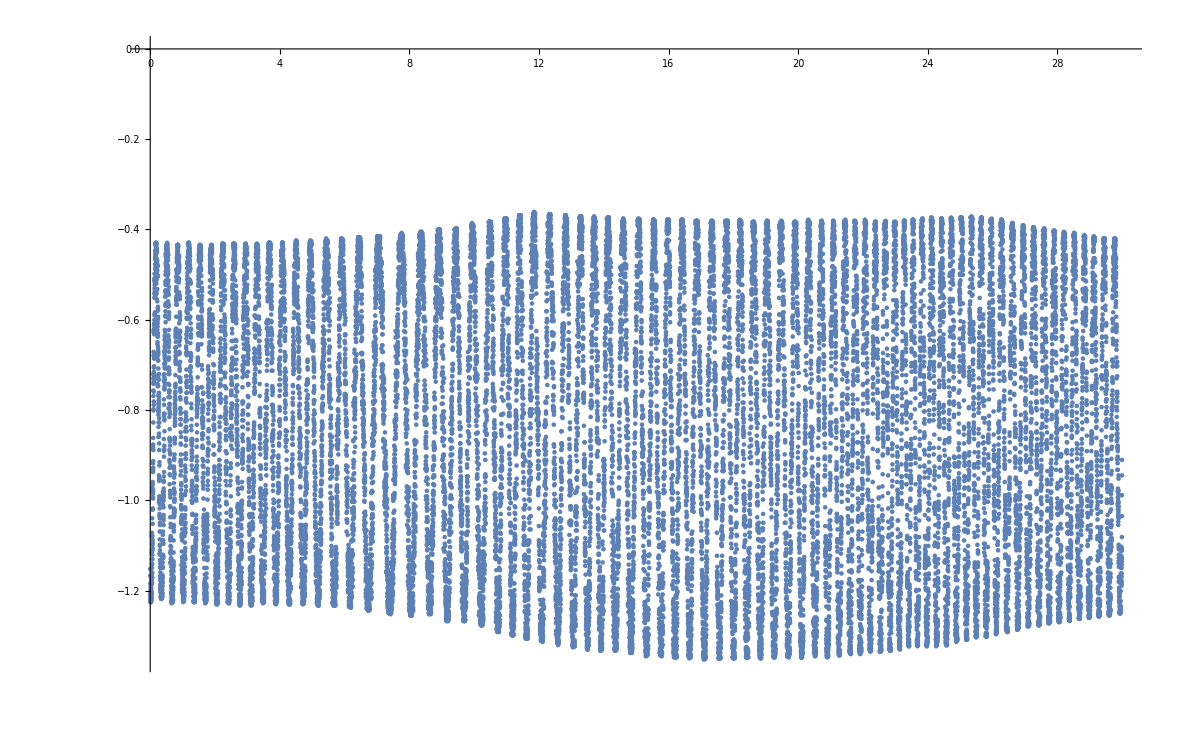

```mathematica
ListPlot[data]
```

```mathematica
v
```

8.33333×10^-7

```mathematica
t=0.409788
```

0.409788

```mathematica
2 v t
```

6.8298×10^-7

```mathematica
minimums=Import["/Users/benxgh1996/Desktop/interferometry/wl_out.csv"]
```

{{1,0.348},{2,0.684},{3,1.02},{4,1.356},{5,1.716},{6,2.052},{7,2.412},{8,2.772},{9,3.108},{10,3.492},{11,3.876},{12,4.284},{13,4.74},{14,5.196},{15,5.676},{16,6.156},{17,6.732},{18,7.404},{19,8.052},{20,8.652},{21,9.18},{22,9.684},{23,10.236},{24,10.716},{25,11.196},{26,11.604},{27,12.084},{28,12.588},{29,13.068},{30,13.5},{31,13.908},{32,14.364},{33,14.868},{34,15.324},{35,15.756},{36,16.212},{37,16.644},{38,17.1},{39,17.58},{40,18.012},{41,18.42},{42,18.828},{43,19.26},{44,19.692},{45,20.1},{46,20.532},{47,20.916},{48,21.276},{49,21.612},{50,21.924},{51,22.212},{52,22.548},{53,22.836},{54,23.124},{55,23.412},{56,23.676},{57,23.988},{58,24.276},{59,24.588},{60,24.9},{61,25.212},{62,25.5},{63,25.812},{64,26.124},{65,26.46},{66,26.796},{67,27.108},{68,27.444},{69,27.732},{70,28.044},{71,28.38},{72,28.692},{73,29.004},{74,29.292},{75,29.604},{76,29.94}}

```mathematica
intervals={}
```

{}

```mathematica
For[i=2,i≤Length[minimums],i++,
AppendTo]
```

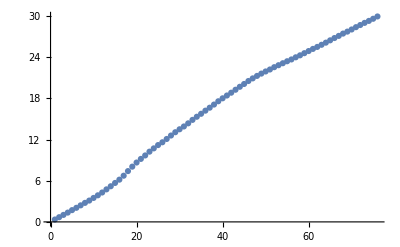

```mathematica
ListPlot[minimums]
```

```mathematica
Fit[minimums,{1, x},x]
```

0.441802+0.409788 x

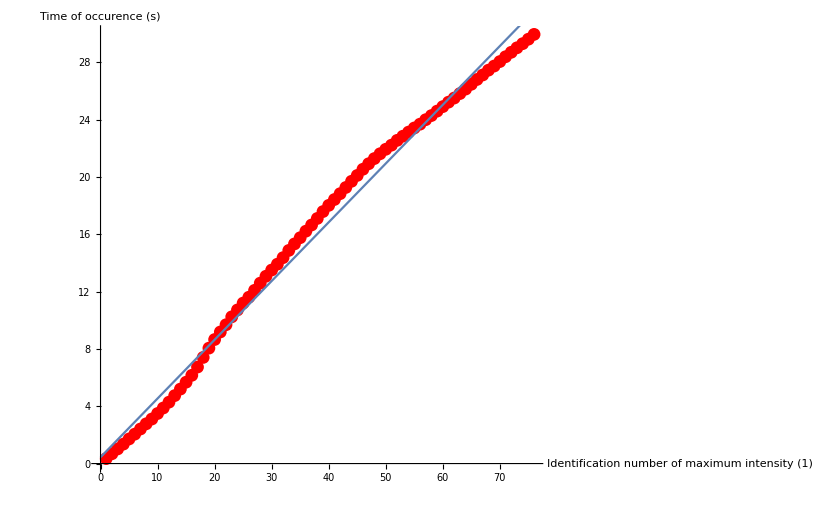

```mathematica
Show[ListPlot[minimums,PlotStyle->Red],Plot[0.44180210526315705+0.40978777853725196 x,{x,0,76}],AxesLabel-> {"Identification number of maximum intensity (1)","Time of occurence (s)"}]
```

```mathematica
Range[2,7]
```

{2,3,4,5,6,7}

```mathematica
2*833.3*0.409788
```

682.953

```mathematica
indexData = Import["/Users/benxgh1996/Desktop/interferometry/air_6.xlsx", {"Data",1,Range[2,5001] ,{1,2}}]
```

{{0.,-0.9985},{0.001,-1.0742},{0.002,-1.1035},{0.003,-1.1084},{0.004,-1.1108},{0.005,-1.1133},{0.006,-1.123},{0.007,-1.0962},{0.008,-1.0303},{0.009,-0.9717},{0.01,-0.9497},{0.011,-0.9717},{0.012,-1.0181},{0.013,-1.0645},{0.014,-1.1011},4971,{4.986,-0.7007},{4.987,-0.6445},{4.988,-0.5713},{4.989,-0.5054},{4.99,-0.4614},{4.991,-0.4395},{4.992,-0.4346},{4.993,-0.4468},{4.994,-0.4663},{4.995,-0.4883},{4.996,-0.5225},{4.997,-0.5664},{4.998,-0.6006},{4.999,-0.5908}}
 |  |  |  |

```mathematica
Length[indexData]
```

5000

```mathematica
p[x_]=(x+8.335)/(0.01+8.335)
```

0.119832 (8.335+x)

```mathematica
For[i=1,i≤Length[indexData],i++,
indexData[[i]][[3]]=p[indexData[[i]][[3]]]]
```

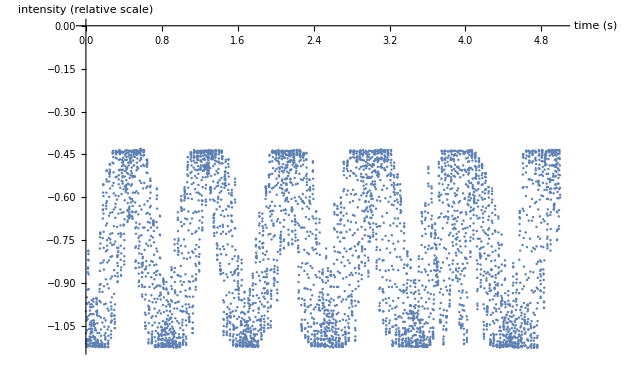

```mathematica
ListPlot[indexData,AxesLabel-> {"time (s)","intensity (relative scale)"},BaseStyle->{FontSize->16}]
```

```mathematica
npData = Import["/Users/benxgh1996/Desktop/interferometry/significant_pressures.xlsx", {"Data",2}]
```

{{1.,0.0134572},{2.,0.0280887},{3.,0.0427202},{4.,0.0567525},{5.,0.0725584},{6.,0.0848412},{7.,0.0977112},{8.,0.114679},{9.,0.128149},{1.,0.0169682},{2.,0.029251},{3.,0.0444697},{4.,0.0596765},{5.,0.0713841},{6.,0.0877651},{7.,0.100635},{8.,0.115267},{9.,0.129311},{10.,0.144518},{11.,0.158562},{1.,0.0169682},{2.,0.0310126},{3.,0.0444697},{4.,0.0579269},{5.,0.0725584},{6.,0.0877651},{7.,0.102397},{8.,0.115854},{1.,0.0146315},{2.,0.0286759},{3.,0.0432954},{4.,0.0573397},{5.,0.0713841},{6.,0.0866028},{7.,0.0994727},{8.,0.112343},{9.,0.127561},{1.,0.0152187},{2.,0.0275015},{3.,0.0409587},{4.,0.0538406},{1.,0.0134572},{2.,0.0280767},{3.,0.042121},{4.,0.0567525}}

```mathematica
npDataCopy = Import["/Users/benxgh1996/Desktop/interferometry/significant_pressures.xlsx", {"Data",2}]
```

{{1.,0.0134572},{2.,0.0280887},{3.,0.0427202},{4.,0.0567525},{5.,0.0725584},{6.,0.0848412},{7.,0.0977112},{8.,0.114679},{9.,0.128149},{1.,0.0169682},{2.,0.029251},{3.,0.0444697},{4.,0.0596765},{5.,0.0713841},{6.,0.0877651},{7.,0.100635},{8.,0.115267},{9.,0.129311},{10.,0.144518},{11.,0.158562},{1.,0.0169682},{2.,0.0310126},{3.,0.0444697},{4.,0.0579269},{5.,0.0725584},{6.,0.0877651},{7.,0.102397},{8.,0.115854},{1.,0.0146315},{2.,0.0286759},{3.,0.0432954},{4.,0.0573397},{5.,0.0713841},{6.,0.0866028},{7.,0.0994727},{8.,0.112343},{9.,0.127561},{1.,0.0152187},{2.,0.0275015},{3.,0.0409587},{4.,0.0538406},{1.,0.0134572},{2.,0.0280767},{3.,0.042121},{4.,0.0567525}}

```mathematica
Length[npData]
```

45

```mathematica
npData == npDataCopy
```

True

```mathematica
Length[npData]
```

45

```mathematica
Fit[npData,{x},x]
```

0.0143445 x

```mathematica
1/0.014344508732550547
```

69.7131

```mathematica
FindFit[npData,a x,{a},{x}]
```

{a→0.0143445}

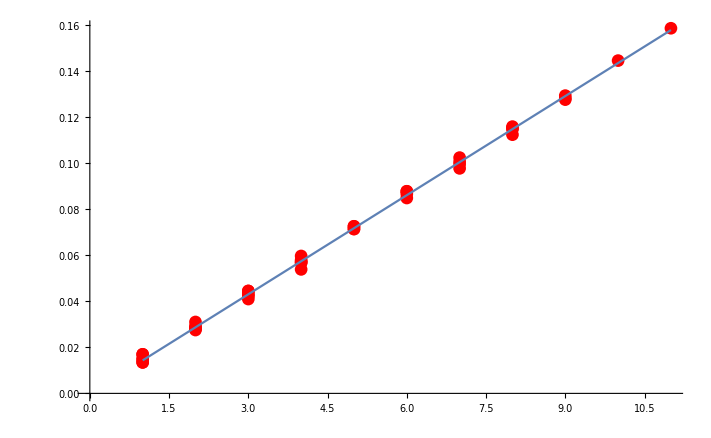

```mathematica
Show[ListPlot[npData,PlotStyle->Red],Plot[a x/.{a->0.014344508732550547},{x,1.,11.}],AxesLabel-> {"Identification number of maximum intensity (1)","ΔP (rap)"}]
```

```mathematica
a/.{a->0.014344508732550547}
```

0.0143445

```mathematica
632.8/(2*100*10^6)*1/0.0143
```

0.000221259

```mathematica
k=0.00022057221052264087
```

0.000220572

```mathematica
k*1+1
```

1.00022

```mathematica
hData = Import["/Users/benxgh1996/Desktop/interferometry/helium_fast_4.xlsx", {"Data",1,Range[2,10001] ,{1,2}}]
```

{{0.,-0.6323},{0.001,-0.5005},{0.002,-0.6226},{0.003,-0.9644},{0.004,-0.9448},{0.005,-0.6299},{0.006,-0.4687},{0.007,-0.5884},{0.008,-0.4639},{0.009,-0.8936},{0.01,-1.1304},{0.011,-0.8447},{0.012,-0.5298},{0.013,-0.9717},{0.014,-0.9692},9971,{9.986,-0.459},{9.987,-0.4565},{9.988,-0.4492},{9.989,-0.4468},{9.99,-0.4492},{9.991,-0.4565},{9.992,-0.4565},{9.993,-0.4443},{9.994,-0.4565},{9.995,-0.5103},{9.996,-0.5615},{9.997,-0.5737},{9.998,-0.5908},{9.999,-0.6201}}
 |  |  |  |

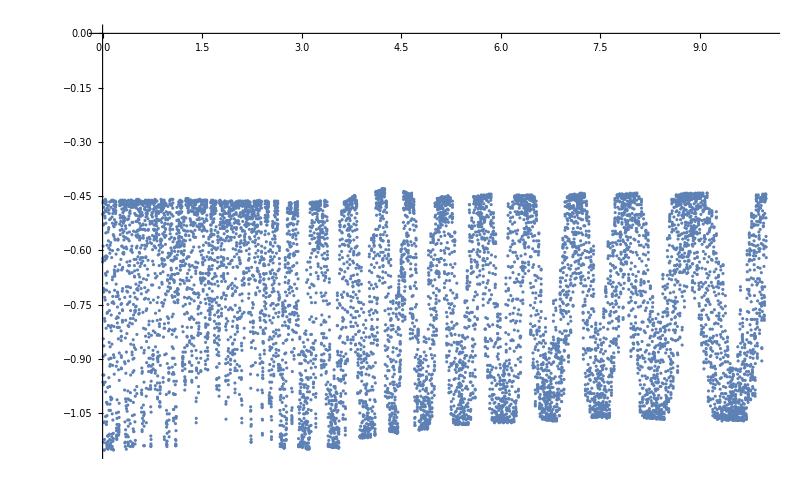

```mathematica
ListPlot[hData]
```

```mathematica
npDataHelium = Import["/Users/benxgh1996/Desktop/interferometry/significant_pressures_helium.xlsx", {"Data",2}]
```

{{1.,0.0491552},{2.,0.101234},{1.,0.0567645},{2.,0.114104},{1.,0.0468185},{1.,0.0234032},{2.,0.061438},{3.,0.104733},{1.,0.0444697},{2.,0.0895267},{1.,0.0479808},{2.,0.0930377}}

```mathematica
FindFit[npDataHelium,b x,{b},{x}]
```

{b→0.0428993}

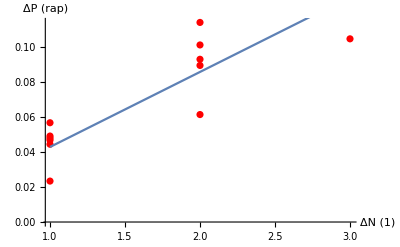

```mathematica
Show[ListPlot[npDataHelium,PlotStyle->Red],Plot[b x/.{b->0.042899255328254726},{x,1.,3.}],AxesLabel-> {"ΔN (1)","ΔP (rap)"}]
```

```mathematica
testList={{1.,0.023403235470341482},{2.,0.061437986818454166},{3.,0.1047333732774117}}
```

{{1.,0.0234032},{2.,0.061438},{3.,0.104733}}

```mathematica
FindFit[testList, c x,c,x]
```

{c→0.0328914}

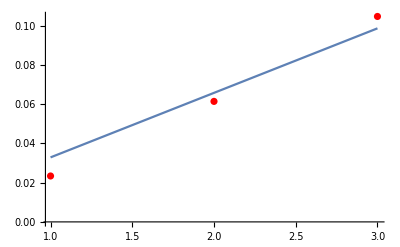

```mathematica
Show[ListPlot[testList,PlotStyle->Red],Plot[c x/.{c->0.03289138063853464},{x,1.,3.}]]
```

```mathematica
632.991/(2*100*10^6)*1/0.0428993
```

0.0000737764

```mathematica
0.0000737764/1.0103
```

0.0000730243

```mathematica
npfDataHelium = Import["/Users/benxgh1996/Desktop/interferometry/significant_pressures_helium.xlsx", {"Data",3}]
```

{{1.,0.0626123},{2.,0.145704},{3.,0.210641},{4.,0.290809},{5.,0.360431},{6.,0.428316},{1.,0.0696225},{2.,0.138083},{3.,0.190749},{4.,0.254524},{5.,0.327082},{6.,0.394368},{7.,0.466339},{8.,0.54006},{9.,0.604422},{10.,0.683415},{11.,0.75831},{1.,0.0713841},{2.,0.126962},{3.,0.194248},{4.,0.24574},{5.,0.320048},{6.,0.388508},{7.,0.462241},{8.,0.528352},{9.,0.602085},{10.,0.67112},{11.,0.748951},{1.,0.0555902},{2.,0.123463},{3.,0.176717},{4.,0.239317},{5.,0.311288},{6.,0.378574},{7.,0.450545},{8.,0.515494},{9.,0.588053},{10.,0.667621}}

```mathematica
FindFit[npfDataHelium,b x,{b},{x}]
```

{b→0.066651}

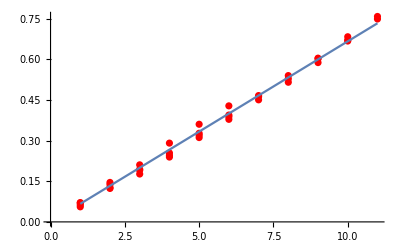

```mathematica
Show[ListPlot[npfDataHelium,PlotStyle->Red],Plot[b x/.{b->0.06665101921825572},{x,1.,11.}],]
```